# N Body Parallel

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
May 18, 2022

## Hyperlink To Documentation for N Body

```mathematica
Hyperlink["NBodySimulation",
"https://reference.wolfram.com/language/ref/NBodySimulation.html"]
```

[NBodySimulation](https://reference.wolfram.com/language/ref/NBodySimulation.html)

## Launch Kernels

```mathematica
CloseKernels[];
LaunchKernels[]
```

## N Body Three Dimensions From Documentation

```mathematica
data=NBodySimulation["InverseSquare",{<|"Mass"->1,"Position"->{0,0,0},"Velocity"->{0,0,0}|>,<|"Mass"->2,"Position"->{1,1,1},"Velocity"->{0,0,0}|>,<|"Mass"->3,"Position"->{1,1,0},"Velocity"->{0,0,0}|>,<|"Mass"->4,"Position"->{0,1,1},"Velocity"->{0,0,0}|>},1]
```

NBodySimulationData[4, <1.>]

```mathematica
ParametricPlot3D[Evaluate[data[All,"Position",t]],{t,0,1}]
```

-Graphics3D-

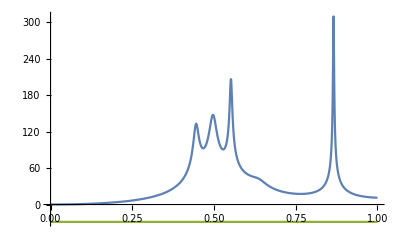

```mathematica
Plot[Evaluate[Map[data[#,t]&,{"TotalKineticEnergy","TotalPairwiseInteractionEnergy","TotalEnergy"}]],{t,0,1},PlotRange->All]
```

```mathematica
data["Equations"]
```

{q_1''[t]==-(2 (q_1[t]-q_2[t]))/((q_1[t]-q_2[t]).(q_1[t]-q_2[t]))^(3/2)-(3 (q_1[t]-q_3[t]))/((q_1[t]-q_3[t]).(q_1[t]-q_3[t]))^(3/2)-(4 (q_1[t]-q_4[t]))/((q_1[t]-q_4[t]).(q_1[t]-q_4[t]))^(3/2),2 q_2''[t]==-(2 (-q_1[t]+q_2[t]))/((-q_1[t]+q_2[t]).(-q_1[t]+q_2[t]))^(3/2)-(6 (q_2[t]-q_3[t]))/((q_2[t]-q_3[t]).(q_2[t]-q_3[t]))^(3/2)-(8 (q_2[t]-q_4[t]))/((q_2[t]-q_4[t]).(q_2[t]-q_4[t]))^(3/2),3 q_3''[t]==-(3 (-q_1[t]+q_3[t]))/((-q_1[t]+q_3[t]).(-q_1[t]+q_3[t]))^(3/2)-(6 (-q_2[t]+q_3[t]))/((-q_2[t]+q_3[t]).(-q_2[t]+q_3[t]))^(3/2)-(12 (q_3[t]-q_4[t]))/((q_3[t]-q_4[t]).(q_3[t]-q_4[t]))^(3/2),4 q_4''[t]==-(4 (-q_1[t]+q_4[t]))/((-q_1[t]+q_4[t]).(-q_1[t]+q_4[t]))^(3/2)-(8 (-q_2[t]+q_4[t]))/((-q_2[t]+q_4[t]).(-q_2[t]+q_4[t]))^(3/2)-(12 (-q_3[t]+q_4[t]))/((-q_3[t]+q_4[t]).(-q_3[t]+q_4[t]))^(3/2)}

```mathematica
data["HamiltonEquations"]
```

{{p_1'[t]==-(2 (q_1[t]-q_2[t]))/((q_1[t]-q_2[t]).(q_1[t]-q_2[t]))^(3/2)-(3 (q_1[t]-q_3[t]))/((q_1[t]-q_3[t]).(q_1[t]-q_3[t]))^(3/2)-(4 (q_1[t]-q_4[t]))/((q_1[t]-q_4[t]).(q_1[t]-q_4[t]))^(3/2),q_1'[t]==p_1[t]},{p_2'[t]==-(2 (-q_1[t]+q_2[t]))/((-q_1[t]+q_2[t]).(-q_1[t]+q_2[t]))^(3/2)-(6 (q_2[t]-q_3[t]))/((q_2[t]-q_3[t]).(q_2[t]-q_3[t]))^(3/2)-(8 (q_2[t]-q_4[t]))/((q_2[t]-q_4[t]).(q_2[t]-q_4[t]))^(3/2),q_2'[t]==p_2[t]/2},{p_3'[t]==-(3 (-q_1[t]+q_3[t]))/((-q_1[t]+q_3[t]).(-q_1[t]+q_3[t]))^(3/2)-(6 (-q_2[t]+q_3[t]))/((-q_2[t]+q_3[t]).(-q_2[t]+q_3[t]))^(3/2)-(12 (q_3[t]-q_4[t]))/((q_3[t]-q_4[t]).(q_3[t]-q_4[t]))^(3/2),q_3'[t]==p_3[t]/3},{p_4'[t]==-(4 (-q_1[t]+q_4[t]))/((-q_1[t]+q_4[t]).(-q_1[t]+q_4[t]))^(3/2)-(8 (-q_2[t]+q_4[t]))/((-q_2[t]+q_4[t]).(-q_2[t]+q_4[t]))^(3/2)-(12 (-q_3[t]+q_4[t]))/((-q_3[t]+q_4[t]).(-q_3[t]+q_4[t]))^(3/2),q_4'[t]==p_4[t]/4}}

## User Defined Mass Position Velocity

```mathematica
massPositionVelocity[mass_,position_,velocity_]:= 
<|"Mass"->mass,"Position"->position,"Velocity"->velocity|>
```

## Timings For Increasing Number of Masses

```mathematica
Table[massPositionVelocity[RandomReal[{1,100}],{RandomReal[{-10,10}],RandomReal[{-10,10}],RandomReal[{-10,10}]},{RandomReal[{-10,10}],RandomReal[{-10,10}],RandomReal[{-10,10}]}],{i,1,10}]
```

{<|Mass→1,Position→{-1.02606,3.0339,-5.54747},Velocity→{-3.24431,9.82032,9.64845}|>,<|Mass→1,Position→{2.38311,-2.29988,6.85355},Velocity→{6.29752,-9.82387,-9.79689}|>,<|Mass→1,Position→{-6.98071,-2.53972,-3.2192},Velocity→{-7.94091,2.4359,-5.70353}|>,<|Mass→1,Position→{2.44843,-7.15551,1.55176},Velocity→{-5.58178,0.769251,0.100416}|>,<|Mass→1,Position→{9.42737,8.3352,-3.61799},Velocity→{-6.93345,5.56669,-4.229}|>,<|Mass→1,Position→{-5.32862,4.2514,6.62103},Velocity→{0.920788,8.21842,-7.02545}|>,<|Mass→1,Position→{0.308958,-2.15807,-1.6026},Velocity→{-5.91178,6.49766,7.81622}|>,<|Mass→1,Position→{-8.88919,4.37844,4.76943},Velocity→{-4.79219,-5.47939,0.656977}|>,<|Mass→1,Position→{0.52798,-1.07925,-1.61274},Velocity→{4.05931,-3.37623,-0.358581}|>,<|Mass→1,Position→{-9.09133,4.94717,8.53385},Velocity→{-6.28555,1.40338,6.77389}|>}

```mathematica
Clear[data]
data= ParallelTable[Timing[ NBodySimulation["InverseSquare",
Table[massPositionVelocity[RandomReal[{1,100}],{RandomReal[{-10,10}],RandomReal[{-10,10}],RandomReal[{-10,10}]},{RandomReal[{-10,10}],RandomReal[{-10,10}],RandomReal[{-10,10}]}],{i,1,j}],1]],{j,2,50}]
```

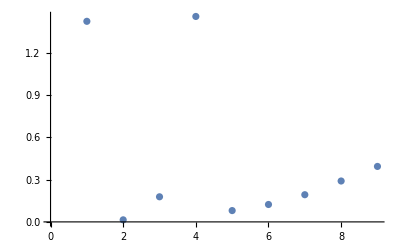

```mathematica
ListPlot[Table[data[[j]][[1]],{j,1,Length[data]}]]
```

```mathematica
Clear[interpolation]
interpolation = 
ListInterpolation[ Table[data[[j]][[1]],{j,1,Length[data]}]]
```

InterpolatingFunction[…]

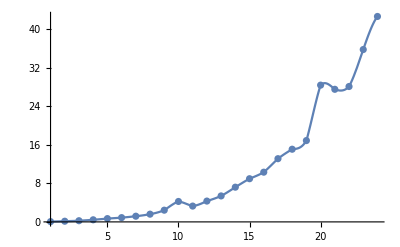

```mathematica
Show[ Plot[interpolation[x],{x,1,Length[data]}] , ListPlot[Table[data[[j]][[1]],{j,1,Length[data]}]] ]
```

```mathematica
ParametricPlot3D[Evaluate[data[[2]][All,"Position",t]],{t,0,1}]
```

-Graphics3D-

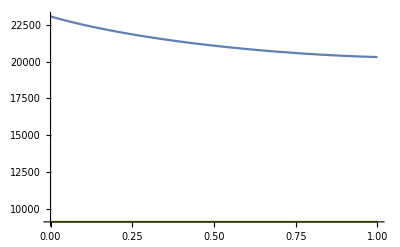

```mathematica
Plot[Evaluate[Map[data[#,t]&,{"TotalKineticEnergy","TotalPairwiseInteractionEnergy","TotalEnergy"}]],{t,0,1},PlotRange->All]
```